## Распределения вероятности и аппроксимация

```mathematica
x=0;
Module[{x},
Set@@Hold[f@x_,x]
];
```

```mathematica
?f
```

```mathematica
Block[{μ,σ,x},
normF[μ_,σ_][x_]=PDF[NormalDistribution[μ,σ],x]
]
```

(ⅇ^(-μ^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
x
```

0

```mathematica
?normF
```

```mathematica
Attributes/@{Set,SetDelayed}
```

{{HoldFirst,Protected,SequenceHold},{HoldAll,Protected,SequenceHold}}

```mathematica
Through[(normF@@@{{1,5},{2,90}})@x]
```

{(ⅇ^(-1/50 (-1+x)^2))/(5 √(2 π)),(ⅇ^(-(-2+x)^2/16200))/(90 √(2 π))}

```mathematica
normF//ClearAll
```

```mathematica
normF[μ_,σ_]=PDF@NormalDistribution[μ,σ]
```

```mathematica
{normF[μ,σ][1],normF[μ,σ][2],normF[μ,σ][3]}
```

```mathematica
Block[{σ,x},
Integrate[
normF[0,σ]@x,
{x,-∞,∞},
Assumptions->σ>0
]
]
```

1

```mathematica
Attributes@Plot
```

{HoldAll,Protected,ReadProtected}

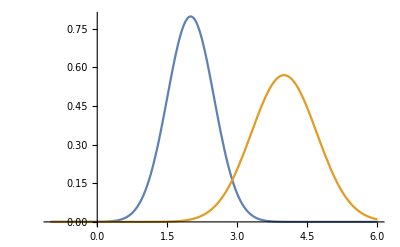

```mathematica
Block[{x},
Plot[
normF[##][x]&@@@{{2,0.5},{4,0.7}}//Evaluate,
{x,-1,6}
]
]
```

```mathematica
dist=MixtureDistribution[{1,0.7},
{NormalDistribution[2,0.5],NormalDistribution[4,0.7]}
];
```

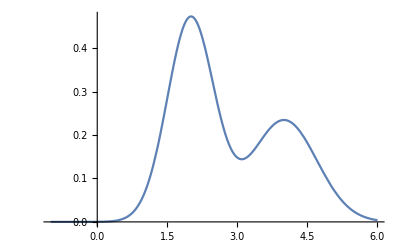

```mathematica
plt=Plot[PDF[dist,x],{x,-1,6}]
```

```mathematica
pts=RandomVariate[dist,1000];
```

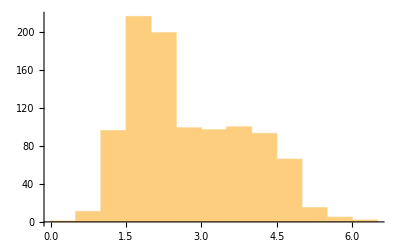

```mathematica
Histogram[pts,15]
```

```mathematica
MinMax@pts
```

{0.406892,6.4328}

```mathematica
dx=0.3;
```

```mathematica
range={Floor@Min@pts,Ceiling@Max@pts,dx};
```

```mathematica
norm[dx_]@ys_:=ys/(dx Total@ys)
```

```mathematica
counts=BinCounts[pts,range]
```

{0,2,6,30,70,109,157,114,95,39,53,65,59,53,60,47,25,9,3,2,1,1,0}

```mathematica
r=Range@@range
```

{0.,0.3,0.6,0.9,1.2,1.5,1.8,2.1,2.4,2.7,3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7,6.,6.3,6.6,6.9}

```mathematica
Length/@{counts,r}
```

{23,24}

```mathematica
data={MovingAverage[r,2],norm[dx]@counts}ᵀ
```

{{0.15,0.},{0.45,0.00666667},{0.75,0.02},{1.05,0.1},{1.35,0.233333},{1.65,0.363333},{1.95,0.523333},{2.25,0.38},{2.55,0.316667},{2.85,0.13},{3.15,0.176667},{3.45,0.216667},{3.75,0.196667},{4.05,0.176667},{4.35,0.2},{4.65,0.156667},{4.95,0.0833333},{5.25,0.03},{5.55,0.01},{5.85,0.00666667},{6.15,0.00333333},{6.45,0.00333333},{6.75,0.}}

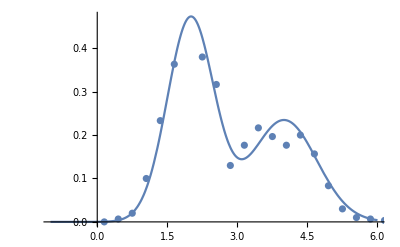

```mathematica
Show[
plt,
ListPlot[data]
]
```